# Diagrama de fase: Rotor pateado

En este notebook graficamos

```mathematica
(*Function to calculateIn[42]:= the next position and momentum*)NextState[θ_,p_]:=Module[{pNext,θNext},
pNext=Mod[p+k Sin[θ],2.π];
θNext=Mod[θ+pNext,2.π];
{θNext,pNext}
]
```

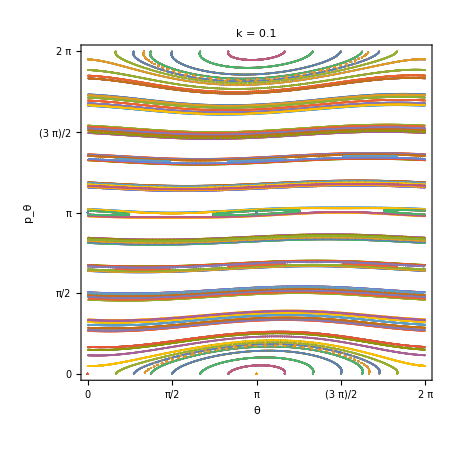

/home/jadeleon/Documents/2023-2/caos_cuantico/k_0_1.png

```mathematica
(*Parameters*)
k=0.1;

(*Function to calculateIn[42]:= the next position and momentum*)NextState[θ_,p_]:=Module[{pNext,θNext},
pNext=Mod[p+k Sin[θ],2.π];
θNext=Mod[θ+pNext,2.π];
{θNext,pNext}
]

(*Evolution of the system*)
t=6;
evolution=Flatten[
Table[
p=p0;θ=θ0;Table[{θ,p}=NextState[θ,p],1000],
{p0,Table[N@((i π)/t),{i,0,2t}]},
{θ0,Table[N@((i π)/t),{i,0,2t}]}],
1];

(*Plotting the phase space*)
ImageToExport=ListPlot[evolution,AspectRatio->1,PlotRange->{{0,2π},{0,2π}},FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,20],Frame->True,FrameTicks->{{{0,Pi/2,Pi,3Pi/2,2Pi},None},{{0,Pi/2,Pi,3Pi/2,2Pi},None}},FrameLabel->{"θ","p_θ"},LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->16],ImageSize->450,PlotLabel->"k = "<>ToString[k]]

(*Export image*)
Export["/home/jadeleon/Documents/2023-2/caos_cuantico/k_"<>#<>".png",ImageToExport]&[StringReplace[ToString[k],"."->"_"]]
```

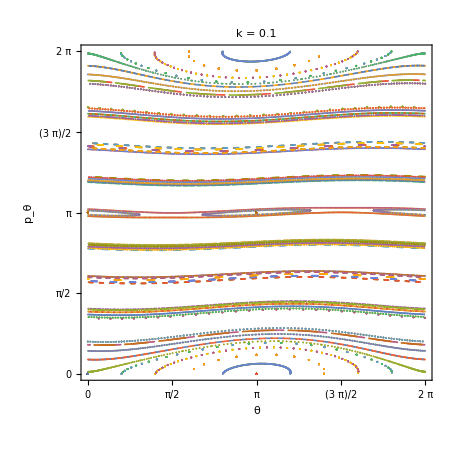

```mathematica
k=0.1;NumberOfSegments=5;NumberOfPoints=250;
trajectories=Flatten[
Table[
p=p0;θ=θ0;
Table[{θ,p}=NextState[θ,p],NumberOfPoints],
{p0,Table[N@((i π)/NumberOfSegments),{i,0,2NumberOfSegments}]},
{θ0,Table[N@((i π)/NumberOfSegments),{i,0,2NumberOfSegments}]}],
1];

ListPlot[trajectories,AspectRatio->1,PlotRange->{{0,2π},{0,2π}},FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,20],Frame->True,FrameTicks->{{{0,Pi/2,Pi,3Pi/2,2Pi},None},{{0,Pi/2,Pi,3Pi/2,2Pi},None}},FrameLabel->{"θ","p_θ"},LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->16],ImageSize->450,PlotLabel->"k = "<>ToString[k]]
```

```mathematica
gif=Table[trajectories=Flatten[
Table[
p=p0;θ=θ0;
Table[{θ,p}=NextState[θ,p],NumberOfPoints],
{p0,Table[N@((i π)/NumberOfSegments),{i,0,2NumberOfSegments}]},
{θ0,Table[N@((i π)/NumberOfSegments),{i,0,2NumberOfSegments}]}],
1];

ListPlot[trajectories,AspectRatio->1,PlotRange->{{0,2π},{0,2π}},FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,28],Frame->True,FrameTicks->{{{0,Pi/2,Pi,3Pi/2,2Pi},None},{{0,Pi/2,Pi,3Pi/2,2Pi},None}},FrameLabel->{"θ","p_θ"},LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->28],ImageSize->1000,PlotLabel->"k = "<>ToString[k]],
{k,kValues}];
Export["/home/jadeleon/Documents/2023-2/caos_cuantico/kicked_rotor.gif",gif]
```

/home/jadeleon/Documents/2023-2/caos_cuantico/kicked_rotor.gif

```mathematica
kValues=Join[Table[k,{k,0.,0.91,0.01}],Table[k,{k,0.92,1,0.001}],Table[k,{k,1,10,0.1}]];
```

## Damped

```mathematica
state[x_,p_]:={p,x-p}
```

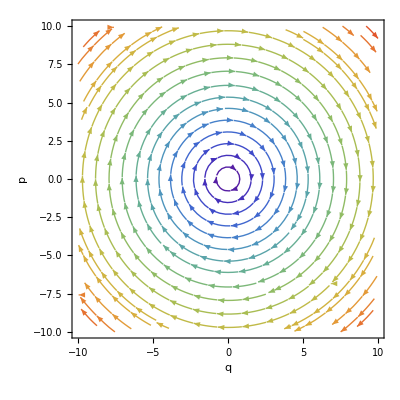

```mathematica
StreamPlot[{p,-q},{q,-10,10},{p,-10,10},StreamColorFunction->"Rainbow",FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,18],Frame->True,FrameLabel->{"q","p"},LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->30],ImageSize->400]
```

```mathematica
Manipulate[StreamPlot[{p,-q-2ξ p},{q,-10,10},{p,-10,10},StreamColorFunction->"Rainbow",FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,18],Frame->True,FrameLabel->{"q","p"},LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->18],ImageSize->400,PlotLabel->"ξ = "<>ToString[ξ]],{ξ,-2,2}]
```

```mathematica
(1-x^2) y-x
```

```mathematica
SHOSolution=DSolve[{x''[t]+ω x[t]==0,x'[0]==v0,x[0]==x0},x[t],t]
```

{{x[t]→(x0 √ω Cos[t √ω]+v0 Sin[t √ω])/(√ω)}}

```mathematica
Clear[q,p,t];
q[t_,q0_,p0_]:=q0  Cos[t ]+p0 Sin[t ]
p[t_,q0_,p0_]:=p0 Cos[t]-q0 Sin[t]
```

```mathematica
D[q0  Cos[t]+p0 Sin[t],t]
```

p0 Cos[t]-q0 Sin[t]

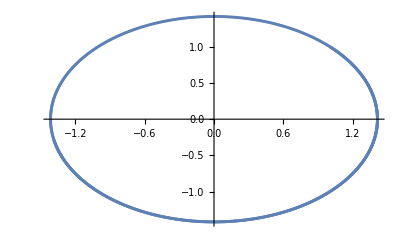

```mathematica
Q=1;P=1;dt=0.01;t=0;
ListPlot[Table[t+=dt;{q[t,Q,P],p[t,Q,P]},1000]]
```

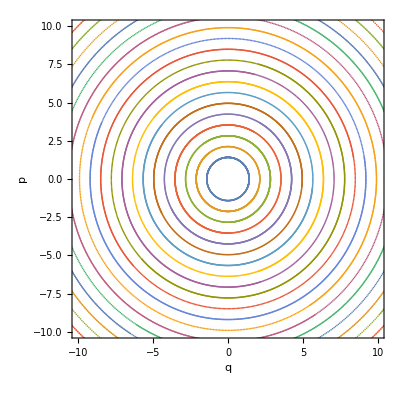

```mathematica
ListPlot[Table[Q=P0;P=P0;Table[t+=dt;{q[t,Q,P],p[t,Q,P]},1000],{P0,1,10,0.5}],AspectRatio->1,PlotRange->{{-10,10},{-10,10}},FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,18],Frame->True,FrameLabel->{"q","p"},LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->30],ImageSize->400]
```